## Introduction to Neural Networks Probability, Energy & the Boltzmann machine

### Initialize

#### Spell check off. Plots small.

```mathematica
Off[General::spell1];
SetOptions[Plot,ImageSize->Small];
SetOptions[ArrayPlot,ColorFunction->Hue,Mesh->True,ImageSize->Tiny];
```

## Introduction

#### The past two lectures

Learning as searching for weights that minimize prediction errors (statistical regression & Widrow-Hoff)

Network dynamics as minimizing “energy” (Hopfield)

One common theme was the analysis of objective functions (e.g. sum of squared differences in regression, or energy in network dynamics) can provide useful insights into neural networks.

We also saw that neurally plausible non-linear dynamics (“update rules”) could reduce the problem of interference on memory recall.

#### Today

Deepen and broaden our conceptual tools by establishing a relationship between “energy” and probability. This will provide an important transition in the development of neural network models and in the material in this course. 

Focus first on constraint satisfaction and seeking a global energy minimum. Then on learning the parameters of a statistical model.

#### Preview of future

By treating neural network learning and dynamics in terms of probability computations, we’ll begin to see how a common set of tools and concepts can be applied to:

1. Inference (as in perception and memory recall): as a process which makes the best guesses given data. What it means to be a “best” is specified in terms of computations on probability distributions (and later in the course, utility functions)

2. Learning: a process that discovers the parameters of a probability distribution

3. Generative modeling: a process that generates data from a probability distribution

## Statistical physics, computation, and statistical inference

Earlier we noted that John von Neumann, one of the principal minds behind the architecture of the modern digital computer, wrote that brain theory and theories of computation would eventually come to more resemble statistical mechanics or thermodynamics than formal logic.  We have already seen in the Hopfield net, the development of the analogy between statistical physics systems and neural networks.  The relationship between computation and statistical physics was subsequently studied by a number of physicists (cf.  Hertz et al., 1991).  We are going to look at a neural network model that exploits the relationship between thermodynamics and computation both to find global minima and to modify weights.  Further, we will see how relating energy to probability leads naturally to statistical inference theory.  Much of the current research in neural network theory grew out of the context of statistical inference (Koch et al., 1986; Knill and Kersten, 1991; Bishop, 1995; Ripley, 1996; MacKay, 2003).

## Probability Preliminaries

We'll go over the basics of probability theory in more detail later in a later lecture. Today we'll review enough to see how energy functions can be related to probability, and energy minimization to maximizing probability.

### Random variables, discrete probabilities, probability densities, cumulative distributions

#### Discrete distributions: random variable X can take on a finite set of discrete values

X = {x(1),...,x(N)]

∑_(i=1)^N p_i=∑_(i=1)^N p(X=x(i))=1

p(X=x) means the probability that random variable X takes on the value x.

#### Continuous densities: X takes on continuous values, x, in some range.

Density: p(x) is analogous to material mass. We can think of the probability over some small domain of the random variable as "probability mass":

prob(x<X<dx+x)=∫_X^(dX+X) p(x)ⅆx
	prob(x<X<dx+x)≃p(x) dx

By analogy with discrete distributions, the area under p(x) must be unity:

∫_(-∞)^∞ p(x)ⅆx=1

like an object always weighing 1.

Cumulative  distribution:

prob (X<x)=∫_(-∞)^x p(x')ⅆx'

Potential confusion alert: We won’t always be consistent about using lower vs. upper case, and will often be loose about notation distinguishing random variables from the values they take on. E.g. sometimes we will write p(X=x) = p(X) when X takes on discrete values. And p(x) for densities. When one needs a specific reminder that different functions represent different distributions, we’ll write p_X(x), and p_Y(y).

#### Densities of discrete random variables

The Dirac Delta function, δ[•], allows us to use the mathematics of continuous distributions for discrete ones, by defining the density as:

p[x]=∑_(i=1)^N p_iδ[x - x[i]], where δ[x - x[i]] ={∞
0 for  x= x[i]
  for  x ≠x[i]

Think of the delta function, δ[•], as ϵ wide and 1/ϵ tall, and then let ϵ -> 0, so that:

∫_(-∞)^∞ δ(y)ⅆy=1

The above density, p[x], is a series of spikes. It is infinitely high only at those points for which x = x[i], and zero elsewhere. But "infinity" is scaled so that the local mass or area around each point x[i], is p_i.

Check out Mathematica's functions: DiracDelta, KroneckerDelta. What is the relationship of KroneckerDelta to IdentityMatrix?

#### Joint probabilities

Prob (X AND Y)=p(X,Y)

Joint density: p(x,y)

Two events, X and Y, are said to be independent if the probability of their occurring together (i.e. their "joint probability") is equal to the product of their probabilities:
	p(X,Y) = p(X)p(Y)

#### Conditional probabilities

Suppose two random variables, X and Y, are independent. What if I told you the value of Y (say Y=y, where y is some specific value)? This would not change your knowledge about the possible values of X.  The intuition is that knowledge of Y provides no help with making statistical decisions about X. Conditional probabilities are written: p(X | Y). If X and Y are independent, then p(X | Y) = p(X). 

Imagine you are blindfolded, and asked to guess who is sitting next to you, i.e. X = ?. If you are in class (Y= “in class“), your guesses would be quite different than if you are at home (Y = “at home”). The conditional probabilities,  p(X = your classmate | you are sitting in class)  and p(X = your classmate | you are sitting at home) are different.

#### Three basic rules of probability

Suppose we know everything there is to know about a set of variables (A,B,C,D,E). What does this mean in terms of probability? It means that we know the joint distribution, p(A,B,C,D,E). In other words, for any particular combination of values (A=a,B=b, C=c, D=d,E=e), we can calculate (e.g. using a formula), look up in a table, or determine using an algorithm, the number p(A=a,B=b, C=c, D=d,E=e).

Deterministic relationships can be treated as special cases.

#### Rule 1: Conditional probabilities from joints: The product rule

Probability about an event changes when new information is gained.
Prob(X given Y) = p(X|Y)

p(X|Y)=(p(X,Y))/(p(Y))

p(X,Y)=p(X|Y) p(Y)

The form of the product rule is the same for densities as for probabilities.

#### Rule 2: Lower dimensional probabilities from joints: The sum rule (marginalization)

p(X)=∑_(i=1)^N p(X,Y(i))

p(x)=∫_(-∞)^∞ p(x,y)ⅆy

#### Rule 3: Bayes' rule

From the product rule, and since p[X,Y] = p[Y,X], we have:

p(Y|X)=(p(X|Y) p(Y))/(p(X)), and using the sum rule, p(Y|X)=(p(X|Y) p(Y))/(∑_Y p(X,Y))

#### Preview

1. Inference: a process which makes guesses given data. Optimal inference makes the best guess according to some model and criterion.

e.g. given data X=x, what value of Y produces the biggest p(Y|X=x)? I.e. the most probable value of Y, given X = x?

2. Learning: a process that discovers the parameters of a probability distribution
Supervised learning: Given training pairs {X_i, Y_i}, what is p(X,Y)? 
Unsupervised learning: Given data {X_i}, what is p(X)?

3. Generative modeling: a process that generates data from a probability distribution

Given p(X), produce sample data {X_i}.

Below we introduce the Boltzmann machine as a historical example of how one can do accomplish all three processes within one network architecture.

## Probability and energy

#### Probabilities of hypotheses contingent on data, Bayes' rule

Conditional probabilities are central to modeling statistical decisions about hypotheses that depend on data. For example, the posterior probability of H, given data d is written:

It is called "posterior", because it is the probability after one has the data. It is more constrained than the prior  probability, p(H). It is called the “prior” because it represents the knowledge one has before having data, or before getting even more data.

If one has a formula for the posterior probability, then it is possible to devise optimal strategies to achieve well-defined goals of inference. For example, imagine the data are given and thus these variables are fixed. A device that picks the hypothesis, H, that makes the posterior probability biggest is optimal in the sense that it makes the fewest errors on average. In this case, the goal is well-defined--to achieve the least average error rate. This kind of decision maker is called a maximum a posteriori  (or MAP) estimator.

Often it is easier to find a formula for p(d | H), then the other way around. In other words, we might have a good idea of the generative model -- p(d|H) and p(H). p(d|H) is called the likelihood and p(H) is the prior.

If the prior p(H) and likelihood are both known, one can do MAP estimation in this case too because of Bayes' rule which tells us the posterior given the prior and the likelihood:

There are two assumptions that can simplify MAP estimation. First, p(d) is  fixed at some constant value (we have the data and so p(d) isn't changing while we try to decide on the best hypothesis to explain the data). Further, we often don't have reason to prefer one hypothesis H=H', over any other, say H=H". So p(H) is constant. If these two conditions hold, then MAP estimation is equivalent to finding the H that makes p(d|H) biggest. This latter strategy is called maximum likelihood estimation.

#### Putting probability and energy together: The Gibbs distribution

Let E(V1,..,Vn) be an energy function for a network, as in a Hopfield model. Then we can write a probability function, called the Gibb's distribution, for the network as:

T is a parameter that controls the "peakedness" of the probability distribution (e.g. later we'll see that if Vs are continuous and the energy is a quadratic function of the V's, the Gibbs distribution becomes a multivariate Gaussian, and if each unit has the same variance, and they are independent, we have T = 2σ2). From the physicist's point of view, T is temperature--e.g. the hotter the matter, the more variance there is in the particle velocities. For a magnetic material, an increase in thermal fluctuations makes it more likely for little atomic magnets to flip out of their otherwise regular arrangement.  κ is a normalization constant determined by the constraint that the total probability over all possible states must equal one. It isn’t always easy to calculate κ, but often we don’t need to.

From a neural perspective, the higher T, the more likely the neuron is to take on values that are not strictly determined by its inputs.

#### If the Hopfield net seeks states that minimize energy, what kind of statistical estimator is the Hopfield net?

Now imagine that some of the values of our units are given and fixed. In other words a subset of the units are declared to be the input, and are "clamped" at specific levels. Call these fixed values Vis. The others, Vi,  can vary. The conditional probability is written as:

So from a statistician's point of view, a network that is evolving to minimize an energy function, is doing  a particular form of Bayesian estimation, MAP. Of course, there is one major caveat-- the network may settle into a local energy minimum, which would correspond to a local probability mode. And a local mode may not be the most probable, just as a local minimum may not be the global minimum.

#### Sidenote on terminology

We've already noted that energy is equivalent to the Lyapunov function of dynamical systems. Other analogous terms you may run into are: Hamiltonian (in statistical mechanics), and cost or objective functions in optimization theory.

## Boltzmann machine: Constraint satisfaction

### Introduction

We've seen how local minima in an energy function can be useful stable points for storing memories. However, for constraint satisfaction problems such as the stereo example, local minima can be a real annoyance--one would like to find the global minimum, because this corresponds to the state-vector that should best satisfy the constraints inherent in the weights and the data input.

One of the early contributions to improving the odds of finding the global minimum was an algorithm called the Boltzmann machine by Ackley et al. (1985). Like the Hopfield network, the Boltzmann machine is a recurrent network with units connected to each other with symmetric weights. The units are binary threshold logic units. 

But there were two key differences. Unlike the 1982 Hopfield net, the Boltzmann machine  uses a stochastic update rule that allows occasional increases in energy. 

More importantly, the Boltzmann machine had a feature that made it a more potentially powerful learning machine. Although fully connected, some units could be "hidden" and others "visible". Similar to the back-prop nets, the hidden units could learn to capture statistical dependencies of higher order than two.

First we take a look at the update rule, and then the learning rule. The learning rule will  lead us to a different view of learning, in which the goal is to model the state of the environment--the joint probability of the various possible combinations of inputs.

### Finding the global minimum: Theory

#### TLUs and energy again

The starting point is the discrete Hopfield net (1982), with a view towards solving constraint satisfaction, rather than memory problems. Energy is then a measure of the extent to which a possible combination of hypotheses violates the constraints of the problem. The stereo problem is an example. Let V1 and V2 be the outputs of neural elements 1 and 2. These two outputs can be thought to represent local  "hypotheses". A positive connection weight (e.g. T12  > 0) means that local hypotheses, V1 and V2 support one another. A negative weight would mean that the two hypotheses inhibit each other--and should discourage both from being accepted at the same time.

Some of the inputs can be clamped (held to a constant value, as in the stereo compatibility matrix below), and the rest allowed to evolve. In this way the network finds the conditional local minimum (or equivalently, the maximum of the corresponding conditional probability).

V_i={V_i^c                      if i is a clamped unit
1                                 if Σ T_ij V_j≥ U_i
0                                 if Σ T_ij V_j< U_i

(Notation: the sum for i<j, is the same as the 1/2 the sum for i not equal to j, because the weight matrix is assumed to be symmetric, and the diagonals are not included. So this may look different than the Hopfield energy, but it isn't.). 
As we have done several times before, we can remove the explicit dependence on the threshold Ui, by including weights -Ui, each with a clamped input of 1 that effectively biases the unit. Then, as we saw for the Hopfield net:

Consider the ith unit. If Vi goes from 1 to 0, the energy gap between two states corresponding to V_i being off (hypothesis i rejected) or on (hypothesis i accepted) is:

#### Boltzmann update rule

Recall that under certain conditions,  Hopfield showed that energy can't increase.

To allow escapes from local minima, the idea is to allow occasional increases  in energy, an idea that goes back to 1953 (Metropolis et al., 1953). So rather than using a hard-threshold to decide whether to output 1 or 0, we use the weighted sum as an input to a probabilistic decision rule, based on the familiar sigmoidal logistic function.   Let's see how it works.

Set

where pi approaches 1, if the weighted sum of the inputs to i (ΔE_i) gets big enough:

Again, T is a free parameter that plays the role of temperature in thermodynamics. 
(Notation alert: T_ij refers to the weights between neuron j and i, and T to the temperature. Completely different meanings for T!)
When we implement the algorithm below, we draw a (uniformly distributed) number between 0 and 1 "out of a hat", and if that number is less than pi =  p(ΔE_i) we set Vi to 1. Otherwise, set it to zero. Specifically, the update rule is:

If the temperature is very low (T about zero), the update rule is the same as that for a deterministic TLU. This is because if the weighted sum of inputs is way bigger than zero, so p is virtually at 1. The probability of setting V to 1 is then guaranteed. If the weighted sum is less than zero, p is zero, and the probability of setting V to 1 is nil.

```mathematica
boltz[x_,T_] := 1/(1 + Exp[-x/T]);
```

Here is a plot of pi, with a high and low temperatures:

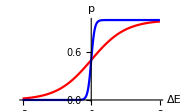

```mathematica
Plot[Tooltip[{boltz[x,0.5],boltz[x,0.05]}],{x,-2,2},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]},AxesLabel->{"ΔE","p"}]
```

#### Simulated annealing

Now if we just let the Boltzmann rule update the state vector at a high temperature, the network will never settle to a stable point in state space. Conversely, if we set the temperature low, the network is likely to get stuck in a local minimum. The key idea behind introducing the notion of temperature is to start off with a high temperature, and then gradually ‘cool’ the network. This simulates the physical process of annealing a material such as steel. If one heats metal, and then cools it rapidly, there is less  crystalline structure or alignment of the  atoms. This is a high energy state, and is desirable for making strong metal. The steel has been tempered. Slower cooling allows the substance to achieve a lower energy state with more alignment, with correspondingly more potential fractures. Although bad for metal strength, slow annealing is good for constraint satisfaction problems.

The update rule is similar to the "Gibbs Sampler" is a general form of updating for  n-valued nodes making up a Markov Random Field (Geman and Geman, 1984). It has been shown that a suitably slow annealing schedule will guarantee convergence (Geman and Geman, 1984):

This annealing schedule, however, can be VERY slow, in fact too slow to be usually practical, except for small scale problems.

Both Boltzmann machine updating and gibbs sampling are examples of Markov chain Monte Carlo (MCMC) methods.

### Local minimum demonstration

Let's look at a simple example where the standard discrete Hopfield net gets stuck in a local minimum, but the Boltzmann machine with annealing gets out of it. We'll construct in a 2D grid (similar to the stereo example). Each unit gets connected to its four nearest neighbors (left, right, above, below) with weights given by weight (=1). As illustrated in an exercise below, the global minimum for this network is when all the units are turned off. But does the TLU update rule get us there from all initial states?

#### Initialization

We will use a toroidal geometry to keep the programming simple.

```mathematica
Mod2[x_,n_] := Mod[x-1,n] + 1;
threshold[x_] := N[If[x>=0,1,-1]];
```

```mathematica
weight = 1;
size = 16;
numiterations = 10;
```

Below, we will deliberately construct a weight matrix so that the energy function has a local minimum at the following state vector:

```mathematica
V = Table[-1,{i,size},{j,size}];

V[[2,3]] = 1; V[[2,4]]= 1;  V[[2,5]] = 1;
V[[3,3]] = 1; V[[3,4]] = 1; V[[3,5]] = 1;
V[[4,3]] = 1; V[[4,4]] = 1; V[[4,5]] = 1;
```

Here is a picture of the state vector with the local minimum:

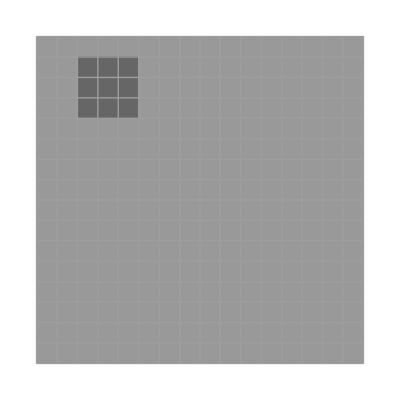

```mathematica
ArrayPlot[V,PlotRange->{-5,5},Mesh->All]
```

#### Asynchronous updating without annealing: Getting stuck

Each unit is connected to its four nearest neighbors with weights given by weight (=1). The rest of the weights are zero. So the update rule is:

```mathematica
update[Vv_,ii_,jj_] := 
			threshold[weight (Vv[[ Mod2[ii + 1,size],
			 jj  ]] +
			Vv[[  Mod2[ii - 1,size], jj  ]] +
			Vv[[  ii, Mod2[jj - 1,size]   ]] +
			Vv[[  ii,  Mod2[jj + 1,size]   ]])];
```

```mathematica
iter=1;
```

```mathematica
gg0=Dynamic[ArrayPlot[V,PlotRange->{-5,5},Mesh->All,ImageSize->Small]]
```

```mathematica
updateAndPlot :=Module[{},For[i=1,i≤size size,i++,iindex=RandomInteger[size-1]+1;jindex=RandomInteger[size-1]+1;V⟦iindex,jindex⟧=update[V,iindex,jindex];];
ArrayPlot[V,PlotRange->{-5,5},Epilog->Inset[iter++,{size-2,size-2}]]];
```

```mathematica
Button["Update and Plot",updateAndPlot]
```

Update and Plot

nothing is happening...not very interesting! 

This makes sense considering the TLU update rule: 

	threshold[x_] := If [sum of four nearest neighbors >=0,1,-1]
	
Nodes in the middle of our 3x3 square have a sum of 4, nodes near the corners have a sum of 0, and the rest have a sum of 2 -- each sum is bigger than or equal to zero.

#### Asynchronous updating with annealing: Getting unstuck

```mathematica
temp0=1;
iter=1;
temp=temp0/Log[1+iter];
```

```mathematica
gg0b=Dynamic[ArrayPlot[V,PlotRange->{-5,5},Mesh->All,ImageSize->Small]]
```

```mathematica
updateAndPlotAnneal :=Module[{},
temp=temp0/Log[1+iter];
For[i=1,i≤size size,i++,iindex=RandomInteger[size-1]+1;jindex=RandomInteger[size-1]+1;
pdeltaE=N[boltz[weight (V⟦Mod2[iindex+1,size],jindex⟧+V⟦Mod2[iindex-1,size],jindex⟧+V⟦iindex,Mod2[jindex-1,size]⟧+V⟦iindex,Mod2[jindex+1,size]⟧),temp]];V⟦iindex,jindex⟧=If[pdeltaE≥RandomReal[],1,-1];];

ArrayPlot[V,PlotRange->{-5,5},Epilog->Inset[iter++,{size-2,size-2}]]];
```

```mathematica
Button["Update with Annealing and Plot",updateAndPlotAnneal]
```

Update with Annealing and Plot

Optional exercise 1: Energy function

Write a function to calculate the energy function for the above network.
What is the energy of the ground state?
What is the energy of the local minimum we constructed above?

Optional exercise 2 : Thermal equilbrium

Make two versions of the above simulation in which 1) the temperature is fixed; 2) the temperature is gradually lowered (as above). Start with a random initial setting of the network.

## Boltzmann Machine: Learning

We've seen how a stochastic update rule improves the chances of a network evolving to a global minimum. Now let's see how learning weights can be formulated as a statistical problem.

#### The Gibbs distribution again

Suppose T is fixed at some value, say T=1. Then we could update the network and let it settle to thermal equilibrium, a state characterized by some statistical stability, but with occasional jiggles. Let Vα represent the vector of neural activities. The probability of a particular state α is given by:

Recall that the second equation is the normalization constant the ensures that the total probability (i.e. over all states) is 1.

We divide up the units into two classes: hidden and visible units. Values of the visible units  are determined by the environment. If the visible units are divided up into "stimulus" and "response" units, then the network should learn associations  and is supervised learning. 

If the visible units are “just watching”, this is unsupervised learning. In this case the visible units are stimulus units, and the network observes and organizes its  interpretation of the stimuli that arrive. 

Consider the goal to have the hidden units discover the structure of the environment. Once learned, if the network was left to run freely, the visible units would take on values that reflect the structure of the environment they learned. In other words, the network has a generative model of the visible structure. This is like dreaming.

Consider two probabilities over the visible units, V:
	P(V) - probability of visible units taking on certain values determined by the environment.
	P'(V) - probability that the visible units take on certain values while the network is running at thermal equilibrium. 

If the hidden units have actually "discovered" the structure of the environment, then the probability P should match P'. How can one achieve this goal? Recall that for the Widrow-Hoff and  error backpropagation rules, we started from the constraint that the network should minimize the error between the network's prediction of the output, and the actual target values supplied during training. We need some measure of the discrepancy between the desired and target states for the Boltzmann machine. 

We need a way of measuring how far apart two probability distributions are from each other--how far P is from P'. One such function is the Kullback-Leibler (KL) divergence measure or relative entropy (also known as the  "Gibbs G measure").

Then we need a rule to adjust the weights so as to bring P' -> P in the sense of reducing the KL measure G. Ackley et al. derived the following rule for updating the weights so as to bring the probabilities closer together. Make weight changes ΔT_ijsuch that:

where p_ij is the probability of V_i and V_j both being 1 when environment is clamping the states at thermal equilibrium averaged over many samples. p'_ij is the probability of V_i and V_jbeing 1 when the network is running freely without the environment at equilibrium.

## Relatives and descendants of Boltzmann machines

As noted above, convergence through simulated annealing can be impractically slow. The mean field approximation is one technique used to improve convergence (cf. Ripley, 1996). Mean field methods also come from physics where one works with the average values of nodes, similar to the transition from the discrete to analog Hopfield networks. 
Boltzmann machines can be considered a special case of belief networks which we will study later (Ripley, 1996). Learning, as you might imagine, is also very slow because of the need to collect lots of averages before doing a weight update.

The Boltzmann machine learns to approximate the joint probability distribution on a set of binary random variables. Some of the variables are designated inputs, and others outputs. Learning large scale joint distributions is known to be a hard problem in statistics. We’ll discuss the general problem later.  The success of the Boltzmann machine has been limited to small scale problems. One successor to the Boltzmann machine is the Helmholtz machine and its derivatives (Dayan et al., 1995; Hinton, 1997). 

A special case called Restricted Boltzmann Machines (RBMs) have been shown to be very useful for a number of problems. RBMs are divided up into layers of units that have  connections between nearby layers but not within layers. RBMs have been used to discover efficient representations of inputs that can then be fine tuned for a task, such as digit classification, using backpropagation (Hinton, G. E., & Salakhutdinov, R. R., 2006).

#### Gibbs sampling

Texture modeling has received considerable attention in biological vision and computer graphics. A recent advance in learning pattern distributions is the Minimax theory (Zhu and Mumford, 1997). Here is an observed sample:

Here is a synthesized sample after Minimax entropy learning:

In general, it is a hard problem to draw true samples from high dimensional spaces. One needs a quantitative model of the distribution and a method such as Gibbs sampling to draw samples.  And in the above text example, the sample was not drawn from an explicit probability distribution.

For a recent example of an application of texture synthesis to understanding the networks of the brain’s visual system, see Freeman, J & Simoncelli, E. P. (2011)

Often it isn’t important to be sure that one has a “true sample”, and other techniques can be used to produce random patterns. E.g. one can first draw sample of white noise, and then iteratively adjust the texture to match statistics of the model, e.g. http://www.cns.nyu.edu/~lcv/texture/

#### Sleep-wake algorithms & “deep belief” networks.

For a computational example of an application to learning and inference, see:

http://www.cs.toronto.edu/~hinton/digits.html

And for a related neuroscience study see: Berkes, P., Orbán, G., Lengyel, M., & Fiser, J. (2011). Spontaneous cortical activity reveals hallmarks of an optimal internal model of the environment. Science, 331(6013), 83–87

## References

Ackley, D. H., Hinton, G. E., & Sejnowski, T. J. (1985). A learning algorithm for Boltzmann machines. Cognitive Science, 9, 147-169.
Besag, J. (1972). Spatial interaction and the statistical analysis  of lattice systems. {\it Journal of the Royal Statistical Society B}, {\bf 34}, 75-83.
Bishop Pattern, Christopher M. (2006) Recognition and Machine Learning. Springer.
Clark, James J. & Yuille, Alan L. (1990) Data fusion for sensory information processing systems. Kluwer Academic Press, Norwell, Massachusetts.
Cross, G. C., & Jain, A. K. (1983). Markov Random Field Texture Models. IEEE Trans. Pattern Anal. Mach. Intel., 5, 25-39.
Geiger, D., & Girosi. (1991). Parallel and Deterministic Algorithms from MRF's:  Surface Reconstruction. I.E.E.E PAMI, 13(5).
D. Geiger, H-K. Pao, and N. Rubin (1998). Organization of Multiple Illusory Surfaces.  Proc. of the IEEE Comp. Vision and Pattern Recognition, Santa Barbara.
Geman, S., & Geman, D. (1984). Stochastic relaxation, Gibbs  distributions, and the Bayesian restoration of images. I.E.E.E. Transactions Pattern Analysis and Machine Intelligence, PAMI-6, 721-741.
Dayan, P., Hinton, G. E., Neal, R. M., & Zemel, R. S. (1995). The Helmholtz Machine. Neural Computation, 7(5), 889-904.
Berkes, P., Orbán, G., Lengyel, M., & Fiser, J. (2011). Spontaneous cortical activity reveals hallmarks of an optimal internal model of the environment. Science, 331(6013), 83–87. doi:10.1126/science.1195870
Freeman, J & Simoncelli, E. P. (2011) Metamers of the ventral stream. Nature Neuroscience, 14, 1195-1201.
Hertz, J., Krogh, A., & Palmer, R. G. (1991). Introduction to the theory of neural computation (Santa Fe Institute Studies in the Sciences of Complexity ed.). Reading, MA: Addison-Wesley Publishing Company.
Hinton, G. E., & Ghahramani, Z. (1997). Generative models for discovering sparse distributed representations. The Philosophical Transactions of the Royal Society, 352(1358), 1177-1190.
Hinton, G. E., Osindero, S. and Teh, Y. (2006) A fast learning algorithm for deep belief nets. Neural Computation 18, pp 1527-1554
Hinton, G. E., & Salakhutdinov, R. R. (2006). Reducing the Dimensionality of Data with Neural Networks. Science, 313(5786), 504–507. doi:10.2307/3846811?ref=no-x-route:854a1d61786ac426bc7d1b8724c03975
Kersten, D. (1990). Statistical limits to image understanding. In C. Blakemore (Ed.), Vision: Coding and Efficiency, (pp. 32-44). Cambridge, UK: Cambridge University Press.
Kersten, D. (1991) Transparency and the cooperative computation of scene attributes. In {Computation Models of Visual Processing}, Landy M., & Movshon, A. (Eds.), M.I.T. Press, Cambridge, Massachusetts.
Kersten, D., & Madarasmi, S. (1995). The Visual Perception of Surfaces, their Properties, and Relationships. DIMACS Series in Discrete Mathematics and Theoretical Computer Science, 19, 373-389.
Knill, D. C., & Kersten, D. K. (1991). Ideal Perceptual Observers for  Computation, Psychophysics, and Neural Networks. In R. J. Watt (Ed.), Pattern Recognition by Man and Machine, (Vol. 14, ): MacMillan Press.
Knill, D. & Richards W(1996). Perception as Bayesian inference.  Cambridge University Press.
Knill, D. C., Kersten, D., & Yuille, A. (1996). A Bayesian Formulation of Visual Perception. In K. D.C. & R. W. (Eds.), Perception as Bayesian Inference, (pp. Chap. 1): Cambridge University Press.
Koch, C., Marroquin, J., & Yuille, A. (1986). Analog “neuronal” networks in early vision. Proceedings of the National Academy of Sciences of the United States of America, 83(12), 4263–4267.
Lee, T. S., Mumford, D., & Yuille, A. Texture Segmentation by Minimizing Vector-Valued Energy Functionals: The Coupled-Membrane Model.: Harvard Robotics Laboratory, Division of Applied Sciences, Harvard University.
MacKay, David J. C. (2003) Information Theory, Inference and Learning Algorithms. Cambride University Press.
Madarasmi, S., Kersten, D., & Pong, T.-C. (1993). The computation of stereo disparity for transparent and for opaque surfaces. In C. L. Giles & S. J. Hanson & J. D. Cowan (Eds.), Advances in Neural Information Processing Systems 5. San Mateo, CA: Morgan Kaufmann Publishers.
Marroquin, J. L. (1985). Probabilistic solution of inverse problems. M. I. T. A.I. Technical Report 860. 
Metropolis, N., Rosenbluth, A., Rosenbluth, M., Teller, A., & Teller, E. (1953). Equation of State Calculations by Fast Computing Machines. J. Phys. Chem, 21, 1087.
Mumford, D., & Shah, J. (1985). Boundary detection by minimizing functionals.  Proc. IEEE Conf. on Comp. Vis. and Patt. Recog.,  22-26.
Poggio, T., Gamble, E. B., \& Little, J. J. (1988). Parallel integration of vision modules. {\it Science}, {\bf 242}, 436-440.
Ripley, B. D. (1996). Pattern Recognition and Neural Networks . Cambridge, UK: Cambridge University Press.
Zhu, S. C., Wu, Y., & Mumford, D. (1997). Minimax Entropy Principle and Its Applications to Texture Modeling. Neural Computation, 9(8), 1627-1660.
Zhu, S. C., & Mumford, D. (1997). Prior Learning and Gibbs Reaction-Diffusion. IEEE Trans. on PAMI, 19(11).

© 1998, 2001, 2003, 2005, 2007, 2009, 2011, 2012, 2014 Daniel Kersten, Computational Vision Lab, Department of Psychology,  University of Minnesota.